```mathematica
(*
1
*)
```

```mathematica
y[x_]=Exp[4x]*Sin[3x]+Exp[4x]*Cos[3x]+Exp[2x]
```

ⅇ^(2 x)+ⅇ^(4 x) Cos[3 x]+ⅇ^(4 x) Sin[3 x]

```mathematica
y'''[x]-10*y''[x]+41*y'[x]-50*y[x] // Simplify
```

0

```mathematica
ClearAll
```

ClearAll

```mathematica
(*
2
*)
```

```mathematica
y[x_] = Exp[mx]
```

ⅇ^mx

```mathematica
Solve[12*y'''[x]-5*y''[x]+y[x]==0,m]
```

{}

```mathematica
(*
3
*)
DSolve[{y'[x] == (3*x*y[x])/(y[x]+1),y[-2]== 3},y[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→ProductLog[3 ⅇ^(-3+(3 x^2)/2)]}}

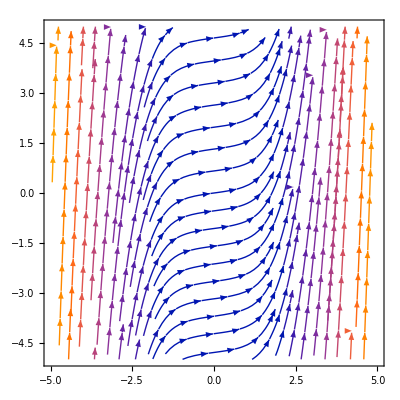

```mathematica
p1 = StreamPlot[{1,ProductLog[3 ⅇ^(-3+(3 x^2)/2)]},{x,-5,5},{y,-5,5}]
```

```mathematica
DSolve[{y'[x] == (3*x*y[x])/(y[x]+1),y[-1]== 2},y[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→ProductLog[ⅇ^((3 x^2)/2+1/2 (-3+2 Log[2 ⅇ^2]))]}}

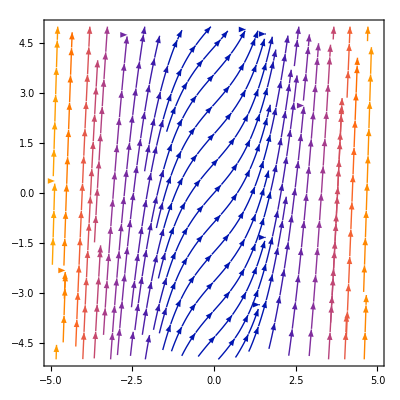

```mathematica
p2 = StreamPlot[{1,ProductLog[ⅇ^((3 x^2)/2+1/2 (-3+2 Log[2 ⅇ^2]))]},{x,-5,5},{y,-5,5}]
```

```mathematica
p3= DSolve[{y'[x] == (3*x*y[x])/(y[x]+1),y[2]== 7},y[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→ProductLog[7 ⅇ^(1+(3 x^2)/2)]}}

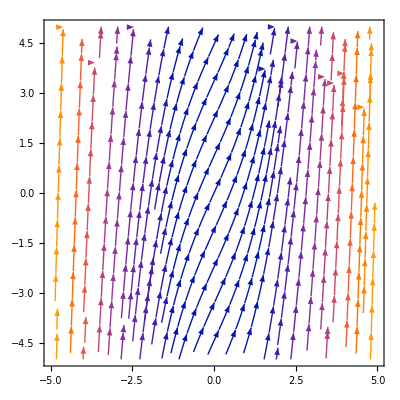

```mathematica
p3 = StreamPlot[{1,ProductLog[7 ⅇ^(1+(3 x^2)/2)]},{x,-5,5},{y,-5,5}]
```

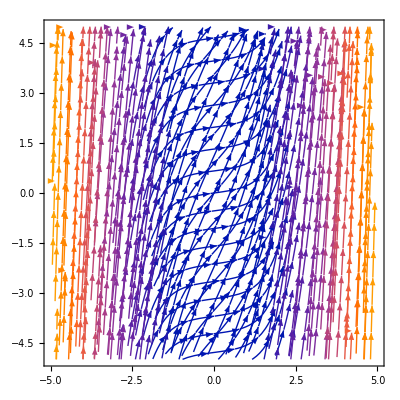

```mathematica
Show[p1,p2,p3]
```

```mathematica
(*
4
*)
```

```mathematica
DSolve[(2*x+6*x*y[x])+(3*x^2+y[x])y'[x] == 0,y[x],x] //Expand
```

{{y[x]→-3 x^2-√(-2 x^2+9 x^4+C[1])},{y[x]→-3 x^2+√(-2 x^2+9 x^4+C[1])}}

```mathematica
DSolve[{Cos[x]y'[x]+Sin[x]*y[x] == Cot[x], y[Pi/6]==2},y[x],x] // Expand
```

{{y[x]→(4 Cos[x])/(√3)+Cos[x] Log[2]+Cos[x] Log[(√3)/2]-Cos[x] Log[Cos[x]]+Cos[x] Log[Sin[x]]}}

```mathematica
DSolve[{(x+1)*y'[x] == x*y[x]^2, y[5]==4},y[x],x] //Expand
```

{{y[x]→-4/(-21+4 x+4 Log[6]-4 Log[1+x])}}

```mathematica
DSolve[{(x+1)*y'[x] == x*y[x]^2, y[5]==4},y[x],x] // Expand
```

{{y[x]→-4/(-21+4 x+4 Log[6]-4 Log[1+x])}}